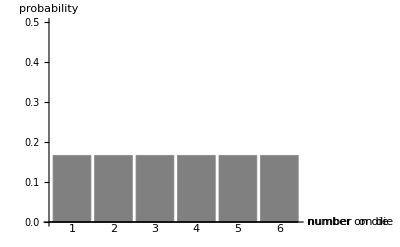

```mathematica
vX = Range[6];
vProbabilityHigherVariance = Table[1/6,{6}];
g1=Show[BarChart[vProbabilityHigherVariance,PlotRange->{Automatic,{0,0.5}},AxesLabel->{"number  on die ","probability "},ChartLabels->vX,BaseStyle->{FontSize->16},ChartStyle->{Gray}],ImagePadding->{{30,100},{30,30}}]
```

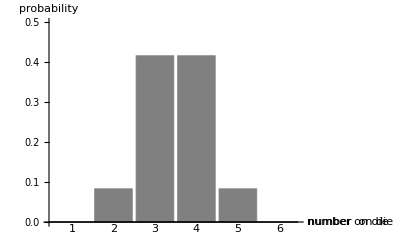

```mathematica
vProbabilityLowerVariance = {0,1/12,1/4+1/6,1/4+1/6,1/12,0};
g2=Show[BarChart[vProbabilityLowerVariance,PlotRange->{Automatic,{0,0.5}},AxesLabel->{"number  on die ","probability "},ChartLabels->vX,BaseStyle->{FontSize->16},ChartStyle->{Gray}],ImagePadding->{{30,100},{30,30}}]
```

```mathematica
toPiecewise[wts_,x_]:=Piecewise[MapIndexed[{#1,x==#2[[1]]}&,wts]]
dLowVariance=ProbabilityDistribution[toPiecewise[vProbabilityLowerVariance,x],{x,1,6,1}];
```

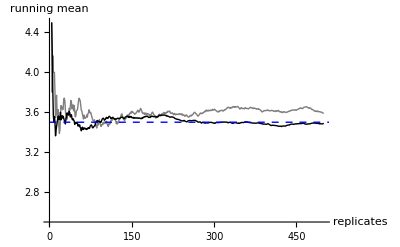

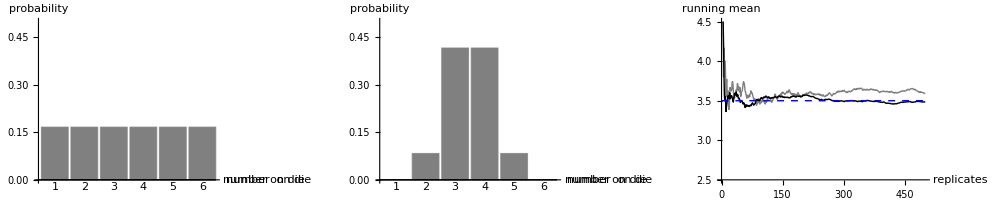

```mathematica
n = 500;
vDataHigh=RandomVariate[DiscreteUniformDistribution[{1,6}],{n}];
vDataLow = RandomVariate[dLowVariance,{n}];
vMeanHigh=Accumulate[vDataHigh]/Table[i,{i,1,n}];
vMeanLow=Accumulate[vDataLow]/Table[i,{i,1,n}];
g3=ListLinePlot[vMeanHigh,PlotStyle->Gray,PlotRange->{Automatic,{2.5,4.5}},Epilog->{Dashed,Blue,Line[{{0,3.5},{1000,3.5}}]},BaseStyle->{FontSize->16},AxesLabel->{"replicates ","running  mean "}];
g4=ListLinePlot[vMeanLow,PlotStyle->Black,PlotRange->{Automatic,{2.5,4.5}},Epilog->{Dashed,Blue,Line[{{0,3.5},{1000,3.5}}]},BaseStyle->{FontSize->16},AxesLabel->{"rolls ","running  mean "}];
g5=Show[g3,g4]
Show[GraphicsRow[{g1,g2,g5}],ImageSize->1000]
```

```mathematica
Variance[DiscreteUniformDistribution[{1,6}]]
```

35/12

```mathematica
Rationalize[Total[Table[(1/6)(i-3.5)^2,{i,1,6}]]]
```

35/12

```mathematica
Variance[dLowVariance]
```

7/12